```mathematica
Clear["Global`*"];
```

```mathematica
<</home/xierr/.Mathematica/Applications/CustomTicks/CustomTicks.m
```

```mathematica
tlen=0.014;tickd=In;thick=Thickness[0.002];ip={{80,30},{60,30}};
```

```mathematica
P[s_,β_]:=(1+β)Gamma[(β+2)/(β+1)]^(β+1)s^β Exp[-Gamma[(β+2)/(β+1)]^(β+1)s^(β+1)];
```

```mathematica
ξsb[ξb_?NumericQ]:=Gamma[ξb+1/2]/Gamma[ξb];
NV[L_?NumericQ,ξb_?NumericQ, f_?NumericQ]:= (1-f)L+((ξsb[ξb]/(√ξb))^-2-1) (L/f)^2;
```

```mathematica
Sigma[data_List,l_]:=N[(Length[data]-1)/Length[data] Variance[BinCounts[data,Append[{-l,l}+MinMax[data],l]]]]
```

```mathematica
cliprange[points_List,xmax_]:=Module[{xmaxpos},xmaxpos=Position[points,Nearest[points[[All,1]],xmax][[1]]][[1,1]];
points[[1;;xmaxpos]]];
```

```mathematica
data=Import["outfile_dailyAdd_L20000.txt","Table"];
```

```mathematica
n=Length[data];
```

```mathematica
eigens=Eigenvalues[data];
```

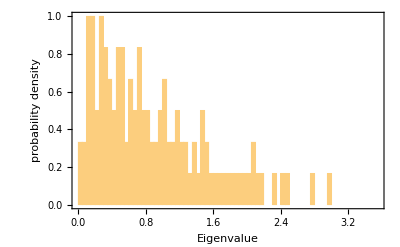

```mathematica
histeigen=Histogram[eigens,200,"PDF",Frame->True,FrameLabel->{Style["StyleBox[\"Eigenvalue\",FontSlant->\"Italic\"]",FontSize->10,FontFamily->"Times New Roman"],Style["probability density",FontFamily->"Times New Roman",Italic,10]}]
```

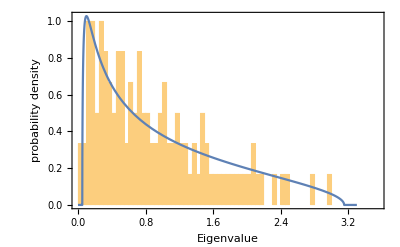

```mathematica
fig=Show[histeigen,Plot[PDF[MarchenkoPasturDistribution[0.6],x],{x,0,3.3},PlotTheme->"Detailed",PlotLegends->None,Exclusions->None]]
```

```mathematica
cumuhistdata=Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[eigens,100,"CDF"]];
```

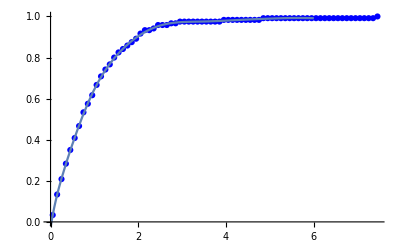

```mathematica
m=15;Nbar[x_]=Fit[cumuhistdata,{1,Sequence@@Table[x^i,{i,1,m}]},x];
Show[ListPlot[cumuhistdata,PlotStyle->Blue,PlotRange->All],Plot[Nbar[x],{x,0,6}]]
```

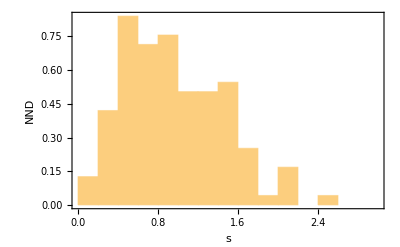

```mathematica
hist=Histogram[Abs[Differences[n Nbar[Sort[eigens]]]],35,"PDF",Frame->True,FrameLabel->{Style["StyleBox[\"s\",FontSlant->\"Italic\"]",FontSize->18,FontFamily->"Times New Roman"],Style["NND",FontFamily->"Times New Roman",Italic,18]}]
```

```mathematica
nnd=Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[Abs[Differences[n Nbar[Sort[eigens]]]],35,"PDF"]];
```

```mathematica
nlmNND=NonlinearModelFit[Select[nnd,#[[1]]≥0&],P[s,β],{β},s]
```

FittedModel[1.52841 ⅇ^(-0.793869 «1») s^0.925264]

```mathematica
beta=N[nlmNND["BestFitParameters"][[1,2]]]
```

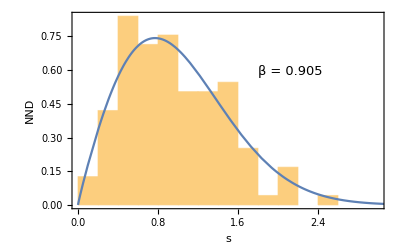

```mathematica
fig1=Show[hist,Plot[nlmNND[s],{s,0,5.0}],Epilog->Text[Style["  β = 0.905",FontSize->13,FontFamily->"Times New Roman"],Scaled[{0.7,0.7}]]]
```

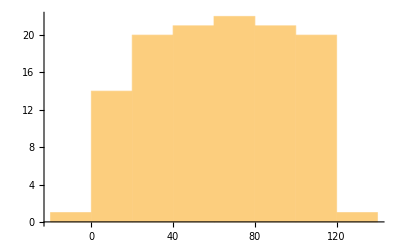

```mathematica
unfoldlamb=Sort[Flatten[n Nbar[eigens]]];
Histogram[unfoldlamb]
```

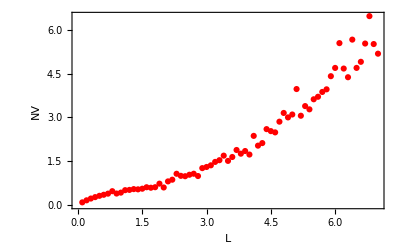

```mathematica
nv=Table[{l,Sigma[unfoldlamb,l]},{l,0.1,7,0.1}];
nvpointstest=ListPlot[Table[{l,Sigma[unfoldlamb,l]},{l,0.1,7,0.1}],PlotRange->All,PlotStyle->Red,Frame->True,FrameLabel->{Style["StyleBox[\"L\",FontSlant->\"Italic\"]",FontSize->18,FontFamily->"Times New Roman"],Style["NV",FontFamily->"Times New Roman",Italic,18]}]
```

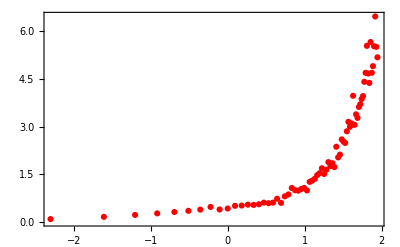

```mathematica
ListPlot[Table[{Log[l],Sigma[unfoldlamb,l]},{l,0.1,7,0.1}],PlotRange->All,PlotStyle->Red,Frame->True]
```

```mathematica
nlmNV=NonlinearModelFit[nv,NV[L,ξb,f],{ξb,f},L];
```

```mathematica
Normal[nlmNV]
```

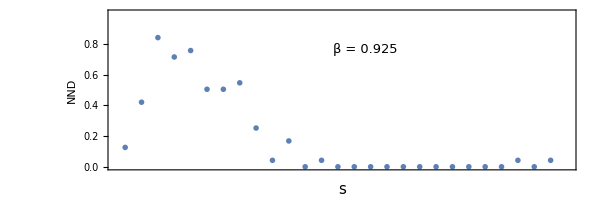

```mathematica
nndpoints=ListPlot[{nnd}(*use your data*),PlotRange->{{0,5.5},{0,1}},AspectRatio->1/3.(*specify the height-to-width ratio*),ImageSize->600,PlotMarkers->{Style["*",Orange,Thick],20},Frame->True,
(*********************Frame Ticks***********************)
ImagePadding->ip,PlotRangeClipping->False,FrameStyle->Directive[thick,Black,FontSize->20,FontFamily->"Times New Roman"],FrameTicksStyle->Directive[thick,"Label", 15],FrameTicks->{{LinTicks[{0,0.2,0.4,0.6,0.8},{0.1,0.3,0.5,0.7,0.9},MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->True,TickDirection->tickd],(*left*)
LinTicks[{0,0.2,0.4,0.6,0.8},{0.1,0.3,0.5,0.7,0.9},MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->False,TickDirection->tickd,ShowTickLabels->False]},(*right*){LinTicks[{0,1,2,3,4,5},{0.5,1.5,2.5,3.5,4.5,5.5},MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->False],(*down*)
LinTicks[{0,1,2,3,4,5},{0.5,1.5,2.5,3.5,4.5,5.5},MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->True]}},(*up*)FrameLabel->{None,Style["NND",FontFamily->"Times New Roman",15]},
(***************************************)PlotLegends->Placed[PointLegend[Automatic,Style[#,10,FontFamily->"Times New Roman"]&/@{"Random"},LegendFunction->Framed,LegendMargins->0],{(*legend position*)Scaled[0.85],Scaled[0.5]}],Epilog->{Text[Style["  β = 0.925",FontSize->13,FontFamily->"Times New Roman"],Scaled[{0.55,0.75}]],Text[Style["StyleBox[\"s\",FontSlant->\"Italic\"]",FontSize->15,FontFamily->"Times New Roman"],Scaled[{0.5,-0.12}]]}]
```

```mathematica
clippoints = Table[{s,Normal[nlmNND]},{s,0.0001,5.5,0.04}] ;
nndmat=ListStepPlot[clippoints,Center,AxesOrigin->{0,0},PlotRange->{{0,3.5},{0,1}},PlotStyle->Lighter[Black],Frame->True];
```

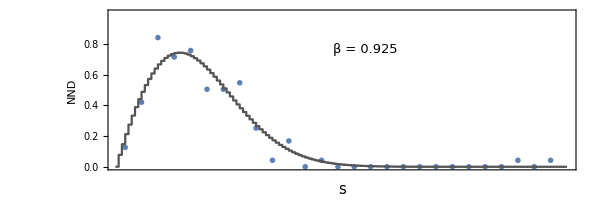

```mathematica
p1=Show[nndpoints,nndmat]
```

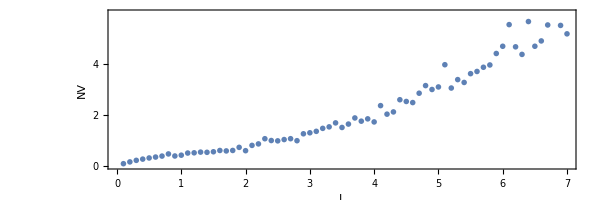

```mathematica
nvpoints=ListPlot[{nv}(*use your data*),PlotRange->{{0,7},{0,6}},DataRange->{{0,7},{0,6}},AspectRatio->1/3.(*specify the height-to-width ratio*),ImageSize->600,PlotMarkers->{Style["*",Orange,Thick],15},Frame->True,
(*********************Frame Ticks***********************)
ImagePadding->ip,FrameStyle->Directive[thick,Black,FontSize->20,FontFamily->"Times New Roman"],FrameTicksStyle->Directive[thick,"Label", 15],FrameTicks->{{LinTicks[Range[0,6,1],Range[0.5,5.5,1],MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->True,ShowLast->False,TickDirection->tickd],(*left*)
LinTicks[Range[0,6,1],Range[0.5,5.5,1],MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->False,TickDirection->tickd,ShowTickLabels->False]},(*right*){LinTicks[Range[0,7,1],Range[0.5,6.5,1],MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->True],(*down*)
LinTicks[Range[0,7,1],Range[0.5,6.5,1],MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->False]}},(*up*)FrameLabel->{Style["StyleBox[\"L\",FontSlant->\"Italic\"]",FontSize->15,FontFamily->"Times New Roman"],Style["NV",FontFamily->"Times New Roman",15]}]
```

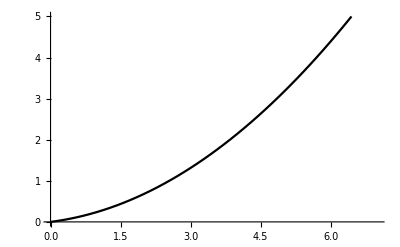

```mathematica
nvcurv=Plot[{Normal[nlmNV]},{L,0,7},PlotStyle->Black,PlotRange->{{0,7},{0,5}}]
```

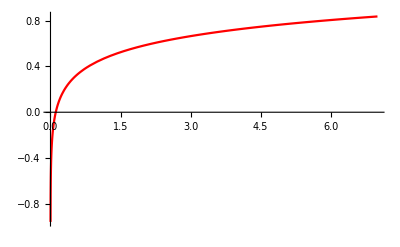

```mathematica
nvcurvGOE=Plot[2/π^2(Log[2π l]+1+EulerGamma-π^2/8),{l,0.001,7},PlotStyle->Red,PlotRange->All]
```

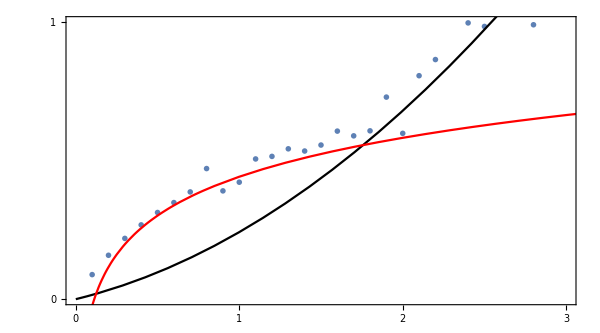

```mathematica
pinset=Show[nvpoints,nvcurv,nvcurvGOE,PlotRange->{{0,3},{0,1.}},FrameLabel->None,AspectRatio->1/1.8,ImagePadding->ip,FrameTicksStyle->Directive[thick,"Label", 8],FrameTicks->{{LinTicks[Range[0,2,1],Range[0.5,1.5,1],MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->True,ShowLast->False,TickDirection->tickd],(*left*)
LinTicks[Range[0,2,1],Range[0.5,1.5,1],MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->False,TickDirection->tickd,ShowTickLabels->False]},(*right*){LinTicks[Range[0,5,1],Range[0.5,4.5,1],MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->True],(*down*)
LinTicks[Range[0,5,1],Range[0.5,4.5,1],MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->False]}}(*up*)]
```

```mathematica
Normal[nlmNV]
```

NV[L,3.59085,0.856023]

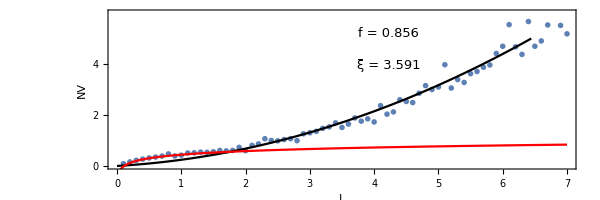

```mathematica
p2=Show[nvpoints,nvcurv,nvcurvGOE,(*we want nvcurv as background*)Epilog->{Text[Style["StyleBox[\"f\",FontSlant->\"Italic\"] = 0.856",FontSize->13,FontFamily->"Times New Roman"],Scaled[{0.6,0.85}]],Text[Style["\!\(\*OverscriptBox[\(ξ\), \(_\)]\) = 3.591",FontSize->13,FontFamily->"Times New Roman"],Scaled[{0.6,0.65}]],Inset[pinset,{0.4,1.78},{0,0},Scaled[1.12]]}]
```

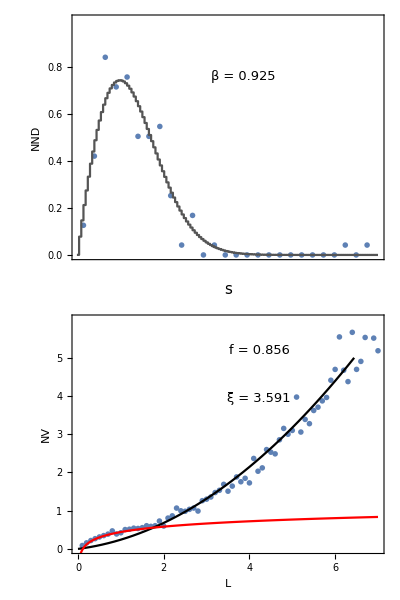

```mathematica
p=Column[{p1,p2},Spacings->-3.5]
```

```mathematica
Export["NNDNV_global_L20000.eps",p]
```

NNDNV_global_L20000.eps